```mathematica
Solve[{ϵ*(1-p)-R0*S*V-R1*S*Ihat-ϵ*S==0,ϵ*p-V==0,R0*S*V+R1*S*Ihat-Ihat==0},{S,V,Ihat}]
```

{{S→(1+p R0+R1-p R1+√(4 (-1+p) R1+(1+p R0+R1-p R1)^2))/(2 R1),V→p ϵ,Ihat→1/2 (ϵ-p ϵ-ϵ/R1-(p R0 ϵ)/R1-(√(4 (-1+p) R1+(1+p R0+R1-p R1)^2) ϵ)/R1)},{S→-(-1-p R0-R1+p R1+√(4 (-1+p) R1+(1+p R0+R1-p R1)^2))/(2 R1),V→p ϵ,Ihat→1/2 (ϵ-p ϵ-ϵ/R1-(p R0 ϵ)/R1+(√(4 (-1+p) R1+(1+p R0+R1-p R1)^2) ϵ)/R1)}}

```mathematica
p=0.4
```

0.4

```mathematica
Clear[p,R]
```

```mathematica
R1=4.5
```

4.5

```mathematica
R0=2.5
```

2.5

```mathematica
Solve[{ϵ*(1-p)-R*S*(V+Ihat)-ϵ*S==0,ϵ*p-V==0,R*S*(V+Ihat)-Ihat==0},{S,V,Ihat}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{S→0.121087,V→0.4 ϵ,Ihat→0.478913 ϵ},{S→1.10114,V→0.4 ϵ,Ihat→-0.501135 ϵ}}

```mathematica
1/2 (ϵ-2 p ϵ-ϵ/R+(√(1-2 R+4 p R+R^2) ϵ)/R)
```

0.453113 ϵ

```mathematica
1/2 (ϵ-2 p ϵ-ϵ/R-(√(1-2 R+4 p R+R^2) ϵ)/R)
```

-0.353113 ϵ

```mathematica
S=0.34688711258507254
```

0.346887

```mathematica
(1+R-√(1-2 R+4 p R+R^2))/(2 R)
```

0.0764365

```mathematica
Clear[S,V,Ihat]
```

```mathematica
(1+p R0+R1-p R1-√(4 (-1+p) R1+(1+p R0+R1-p R1)^2))/(2 R1)
```

0.148882

```mathematica
(-1-p R0-R1+p R1+√(4 (-1+p) R1+(1+p R0+R1-p R1)^2))/(2 R1)
```

-0.148882

```mathematica
1/2 (ϵ-p ϵ-ϵ/R1-(p R0 ϵ)/R1-(√(4 (-1+p) R1+(1+p R0+R1-p R1)^2) ϵ)/R1)
```

-0.295562 ϵ

```mathematica
1/2 (ϵ-p ϵ-ϵ/R1-(p R0 ϵ)/R1+(√(4 (-1+p) R1+(1+p R0+R1-p R1)^2) ϵ)/R1)
```

1/2 (ϵ-ϵ/R1+(√(-4 R1+(1+R1)^2) ϵ)/R1)

```mathematica
ϵ=11/9136
```

11/9136

```mathematica
g[p_]:=1/2 (0.0009364662385678148+0.0002675617824479471 √((5.5-2. p)^2+18. (-1+p))-0.0018729324771356295 p)
```

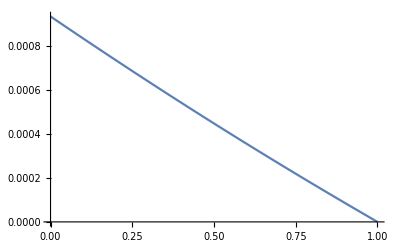

```mathematica
Plot[g[p],{p,0,1}]
```

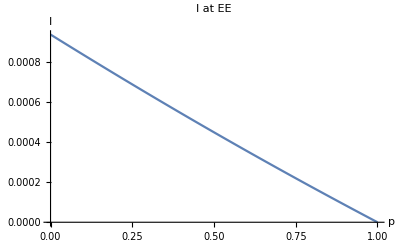

```mathematica
Show[%7,AxesLabel->{HoldForm[p],HoldForm["I"]},PlotLabel->HoldForm["I" at EE],LabelStyle->{GrayLevel[0]}]
```

```mathematica
Export["C:\\Users\\Roger Zhang\\Documents\\GitHub\\RogerZhang\\July_2nd\\Figures\\I_at_EE.pdf",%19,"PDF"]
```

C:\Users\Roger Zhang\Documents\GitHub\RogerZhang\July_2nd\Figures\I_at_EE.pdf